```mathematica
(* a first order ODE where u2[t] is given *)
γ = 1;
U2[t_] := 0.25 Sin[2π t];
x = {-1, 0, 1};
u0 = {0,U2[0],0};
f[t_] := 10{-t, 0, t^2};
tmax = 1.0;
MM = ({{2, 1, 0}, {1, 4, 1}, {0, 1, 2}});
KK = 100({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});
F = ({{1, 0, 0}, {0, 0, 0}, {0, 0, 1}});

soln = NDSolve[{
(MM.{u1'[t], U2'[t], u3'[t]} + KK.{u1[t], U2[t], u3[t]})[[{1,3}]] == f[t][[{1,3}]] ,
u1[0] == u0[[1]],u3[0] == u0[[3]]
}, {u1[t], u3[t]}, {t, 0, tmax}][[1]];
derivatives = {u1'[t]->D[u1[t] /. soln, t], u3'[t]->D[u3[t] /. soln, t]};
```

```mathematica
error[n_] := Module[{dt = tmax/n},
TT=MM+γ KK dt;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];

u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
dudt = LinearSolve[H, f[0] - KK.u - MM.{0, U2'[0], 0}];
dudt[[2]] = U2'[0];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
τ+=dt;
fc=MM.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc -KK.F.(u+ (1-γ)dudt*dt);
rhs[[2]]=0;


dudtprev = dudt;
dudt=LinearSolve[TT,rhs];
dudt[[2]]=U2'[τ];
u+=((1-γ)dudtprev + γ dudt)dt;
u[[2]]=U2[τ];

If[i < 4,
Print[τ];
Print[fc];
Print[KK.F.(u+ (1-γ)dudt*dt)];
Print[rhs];
Print[dudt];
Print[u];
Print[]
];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
error[20]
```

0.05

{-6.23151,21.4265,-6.23151}

{4.09393,-8.56287,4.46893}

{5.73151,0,6.25651}

{0.818787,1.49392,0.893787}

{0.0409393,0.0772542,0.0446893}

0.1

{-13.4238,34.4725,-13.4238}

{10.0439,-20.9806,10.9367}

{8.3299,0,9.0549}

{1.18999,1.2708,1.29356}

{0.100439,0.146946,0.109367}

0.15

{-19.3021,44.144,-19.3021}

{15.5855,-32.6582,17.0727}

{7.75827,0,8.59042}

{1.10832,0.923291,1.2272}

{0.155855,0.202254,0.170727}

{0.00191232,0.,0.00201232}

```mathematica
KK.{0.0818787, 0, 0.0893787}
```

{8.18787,-17.1257,8.93787}

```mathematica
(* for a second order method, we expect the error to reduce by a factor of 4 when halving the timestep (asymptotically) *)
errors = Table[error[2^i * 10], {i, 0, 6}]; errors // MatrixForm
errors[[1;;-2, {1, 3}]]/errors[[2;;-1, {1, 3}]]
```

0.1

{-13.4238,34.4725,-13.4238}

{0.103532,0.146946,0.112699}

0.2

{-23.291,49.4944,-23.291}

{0.19468,0.237764,0.216208}

0.3

{-24.2618,45.6112,-24.2618}

{0.209629,0.237764,0.245716}

0.05

{-6.23151,21.4265,-6.23151}

{0.0409393,0.0772542,0.0446893}

0.1

{-13.4238,34.4725,-13.4238}

{0.100439,0.146946,0.109367}

0.15

{-19.3021,44.144,-19.3021}

{0.155855,0.202254,0.170727}

0.025

{-2.3594,14.0276,-2.3594}

{0.0117189,0.0391086,0.0131425}

0.05

{-6.23151,21.4265,-6.23151}

{0.0370501,0.0772542,0.0405995}

0.075

{-9.95017,28.2979,-9.95017}

{0.0675788,0.113498,0.0736355}

0.0125

{-0.395523,10.1868,-0.395523}

{0.00104047,0.0196148,0.00152725}

0.025

{-2.3594,14.0276,-2.3594}

{0.00875339,0.0391086,0.0100385}

0.0375

{-4.30874,17.7818,-4.30874}

{0.0205165,0.0583613,0.0228037}

0.00625

{0.58809,8.24133,0.58809}

{-0.00154902,0.00981495,-0.00139928}

0.0125

{-0.395523,10.1868,-0.395523}

{-0.000536105,0.0196148,-0.000120679}

0.01875

{-1.37853,12.1165,-1.37853}

{0.00242732,0.0293843,0.00319863}

0.003125

{1.07965,7.26366,1.07965}

{-0.00150122,0.00490842,-0.00145886}

0.00625

{0.58809,8.24133,0.58809}

{-0.00217753,0.00981495,-0.0020559}

0.009375

{0.0963019,9.21583,0.0963019}

{-0.00214009,0.0147177,-0.00190703}

0.0015625

{1.32529,6.77375,1.32529}

{-0.000971676,0.00245433,-0.000960336}

0.003125

{1.07965,7.26366,1.07965}

{-0.00170627,0.00490842,-0.00167303}

0.0046875

{0.833911,7.75287,0.833911}

{-0.00222087,0.00736204,-0.00215592}

(0.00453146 | 0. | 0.00473146
0.00191232 | 0. | 0.00201232
0.000856301 | 0. | 0.000906301
0.000401762 | 0. | 0.000426762
0.000194109 | 0. | 0.000206609
0.0000953402 | 0. | 0.00010159
0.0000472395 | 0. | 0.0000503645)

{{2.36962,2.35125},{2.23323,2.22036},{2.13136,2.12367},{2.06978,2.06556},{2.03596,2.03375},{2.01823,2.0171}}

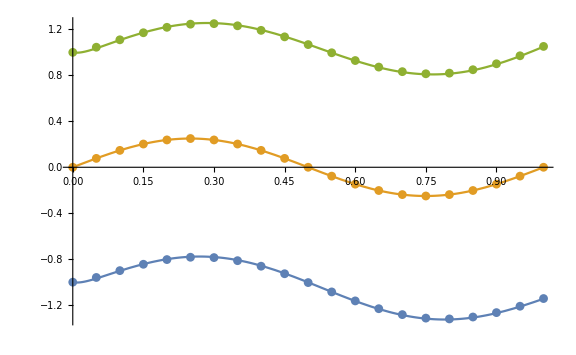

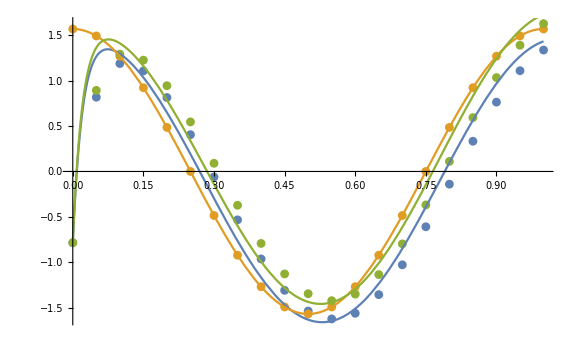

```mathematica
error[20];
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
(* a second order ODE where u2[t] is given *)
γ = 1/2;
β = 1/6;
U2[t_] := 0.25 Cos[2π t]^4;
U2[t_] := 0.25 Sin[2π t];
x = {-1, 0, 1};
u0 = {0,U2[0],0};
dudt0 = {0, U2'[0], 0};
f[t_] := 10{-t, 0, t^2};
tmax = 1.0;
n = 80;
dt = tmax / n;
MM = ({{2, 1, 0}, {1, 4, 1}, {0, 1, 2}});
CC = ({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});
KK = 100({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});


F = ({{1, 0, 0}, {0, 0, 0}, {0, 0, 1}});


soln = NDSolve[{
(MM.{u1''[t], U2''[t], u3''[t]} + CC.{u1'[t], U2'[t], u3'[t]} + KK.{u1[t], U2[t], u3[t]})[[{1,3}]] == f[t][[{1,3}]] ,
u1[0] == u0[[1]], u1'[0] == dudt0[[1]],
u3[0] == u0[[3]], u3'[0] == dudt0[[3]]
}, {u1[t], u3[t]}, {t, 0, tmax}][[1]];
derivatives = {u1'[t]->D[u1[t] /. soln, t], u3'[t]->D[u3[t] /. soln, t]};
```

```mathematica
error[n_] := Module[{dt = tmax/n},
TT=MM+γ CC dt+β KK dt^2;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
u=u0;
dudt=dudt0;
d2udt2 = LinearSolve[H, f[0] - CC.dudt - KK.u - MM.{0, U2''[0], 0}];
d2udt2[[2]] = U2''[0];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
τ+=dt;
fc = MM.{0, U2''[τ], 0}+ CC.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc - CC.F.(dudt+(1-γ)d2udt2 * dt)-KK.F.(u+ dudt*dt+(1/2-β)d2udt2 * dt^2);
rhs[[2]]=0;
If[i < 3,
Print[fc];
Print[CC.F.(dudt+(1-γ)d2udt2 * dt)+KK.F.(u+ dudt*dt+(1/2-β)d2udt2 * dt^2)];
Print[f[τ]];
Print[rhs];
Print[];
];
d2udt2prev = d2udt2;
d2udt2=LinearSolve[TT,rhs];
u+=dudt*dt+((1/2-β)d2udt2prev + β d2udt2)dt^2;
dudt+=((1-γ)d2udt2prev + γ d2udt2)dt;
d2udt2[[2]] = U2''[τ];
dudt[[2]] = U2'[τ];
u[[2]] = U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
error[20]
u
```

{0,0.,0}

{0,1.5708,0}

{0.785398,0.,0.785398}

{-12.2692,6.23918,-12.2692}

{0.0850848,-0.17017,0.0850848}

{-0.5,0,0.025}

{11.6841,0,12.2091}

{-21.7666,8.72603,-21.7666}

{1.87934,-3.8349,1.95555}

{-1.,0,0.1}

{18.8873,0,19.9111}

{-0.00170409,0.,-0.00139308}

{-1.0124,3.82857×10^-16,-0.823848}

```mathematica
(* for a second order method, we expect the error to reduce by a factor of 4 when halving the timestep (asymptotically) *)
errors = Table[error[2^i * 10], {i, 0, 6}];
errors[[1;;-2, {1, 3}]]/errors[[2;;-1, {1, 3}]]
```

{{2.74615,3.20921},{3.68106,3.79344},{3.91966,3.94765},{3.97988,3.98694},{3.995,3.99705},{3.99887,4.00054}}

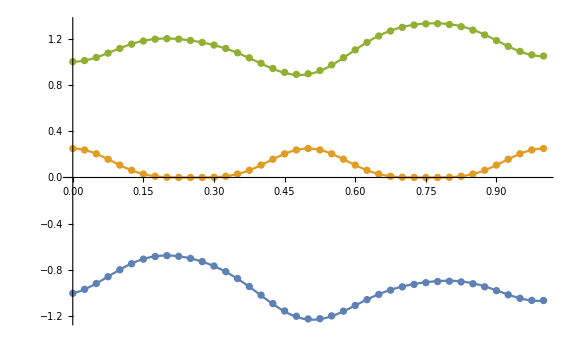

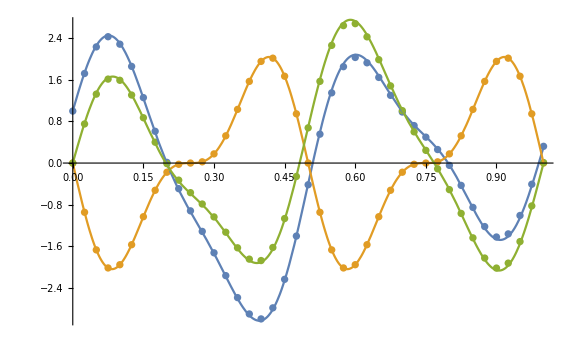

```mathematica
error[40];
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
N[(({u1[t], U2[t], u3[t]}) /. soln) /. t->1, 8]
```

{-0.0635974,0.25,0.0468672}

```mathematica
Inverse[TT]
```

{{0.499058,0.,0.},{0.,1.,0.},{0.,0.,0.499058}}

```mathematica
error[20]
```

{0.00505608,0.,0.00745232}

```mathematica
errorRK2[n_] := Module[{dt = tmax/n, fc},
u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
xHistory={x+u};
vHistory={dudt};
fc[t_] := KK.{0, U2[t], 0}+MM.{0, U2'[t], 0};
Do[
k1 = LinearSolve[H, f[τ] - KK.u - MM.{0, U2'[τ], 0}];
k2 = LinearSolve[H, f[τ+2/3 dt]-KK.F.(u+2/3 k1 dt)-fc[τ + 2/3 dt]];
τ+=dt;
dudt = (1/4 k1 + 3/4 k2);
dudt[[2]] = U2'[τ];
u+=dudt dt;
u[[2]]=U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
```

{0.000014747,0.,0.0000156994}

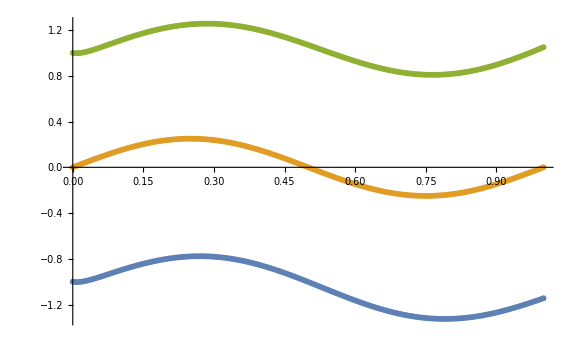

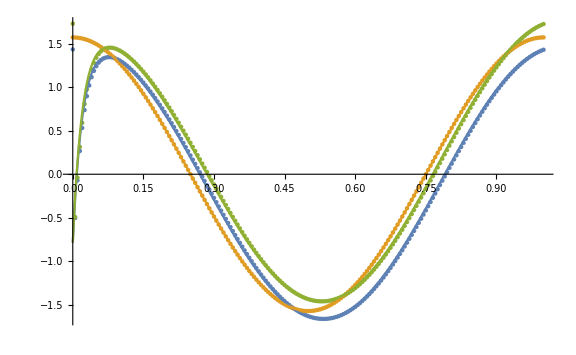

```mathematica
errorRK2[200]
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
errorFE[n_] := Module[{dt = tmax/n},
u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
dudt = LinearSolve[H, f[τ]-KK.u-MM.{0, U2'[τ], 0}];
τ+=dt;
u+=dudt dt;
dudt[[2]] = U2'[τ]; 
u[[2]]=U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
errorFE[100]
errorFE[200]
errorFE[400]
errorFE[800]
```

{-0.000281529,0.,-0.000301529}

{-0.000145297,0.,-0.000155297}

{-0.0000737701,0.,-0.0000787701}

{-0.0000371634,0.,-0.0000396634}

{-0.0000737701,0.,-0.0000787701}

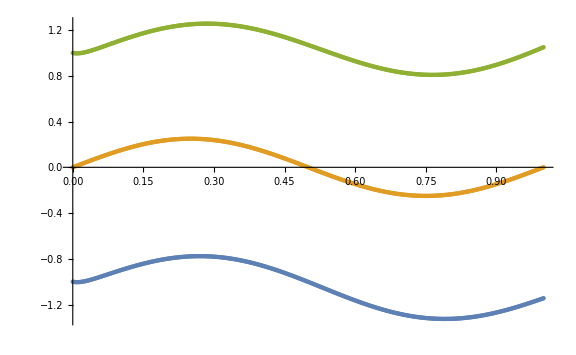

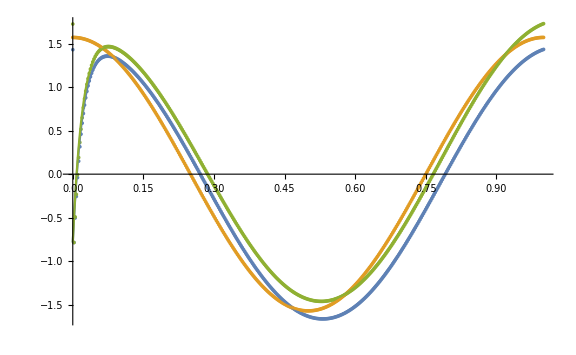

```mathematica
errorFE[400]
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
errorRK4[n_] := Module[{dt = tmax/n, fc},
u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
τ=0;
xHistory={x+u};
vHistory={dudt};
fc[t_] := KK.{0, U2[t], 0}+MM.{0, U2'[t], 0};
Do[
k1 = LinearSolve[H, f[τ] - KK.u - MM.{0, U2'[τ], 0}];
k2 = LinearSolve[H, f[τ+1/2 dt]-KK.F.(u+1/2 k1 dt)-fc[τ +1/2 dt]];
k3 = LinearSolve[H, f[τ+1/2 dt]-KK.F.(u+1/2 k2 dt)-fc[τ+1/2 dt]];
k4 = LinearSolve[H, f[τ+dt]-KK.F.(u+k3 dt)-fc[τ +dt]];
τ+=dt;
dudt = 1/6(k1 + 2k2 + 2 k3 + k4);
dudt[[2]] = U2'[τ];
u+=dudt dt;
u[[2]]=U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]
```

```mathematica
g[t_] := X Sin[2 π t]
```

```mathematica
g'[0.5]
```

-6.28319 X